```mathematica
data:=Import["../fatal-police-shootings-data.csv"]
```

```mathematica
allDates:=data[[2;;, 3]]
dates:=Select[allDates,StringStartsQ[#,{"2015","2016","2017","2018"}]&]
```

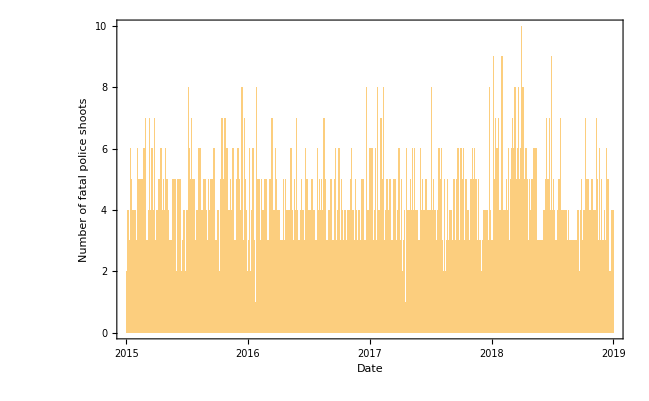

```mathematica
DateHistogram[
dates,"Day",
Frame->{True,True,True,True},
Ticks->{{"2015","2016","2017","2018","2019"},None},
FrameTicks->{Automatic,Range[0,Max[Counts[dates]]]},
FrameLabel->{"Date","Number of fatal police shoots"}
]
```